7.29935

ρc=0.000741111km^-

K=7.29935km^4

Rstar=0.0205444km

Rmax=0.0205444km

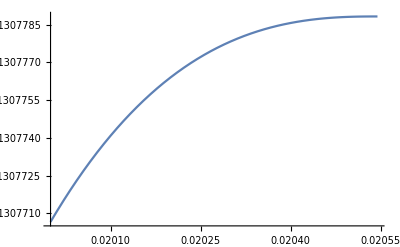

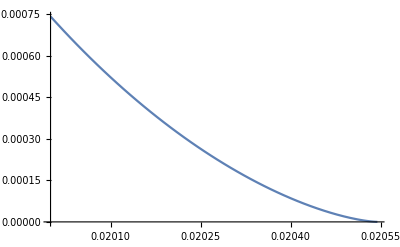

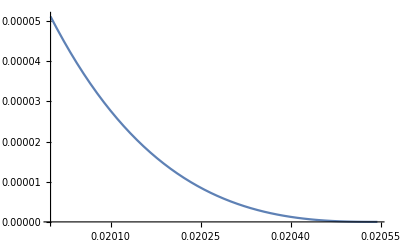

Radius=0.0205444

Mass=0.00931308+1.14584×10^-19 ⅈ

```mathematica
(*m[r]:=4/3 π r^3 ρ0*)
G=6.67*10^(-8);
c=3*10^(10);
my0=0.02;
pc:=1;
κ:=5/3;
K1=5.38*10^9;
ρc1:=10^15;
ρc:=ρc1*G/c^2*(100*10^3)^2;
K=K1*(G c)^(-2/3)*(100*10^3)^(-4/3)
Print["ρc=",ρc,"\!\(\*SuperscriptBox[\"km\",RowBox[List[\"-\",\"2\"]]]\)"];
Print["K=",K,"\!\(\*SuperscriptBox[\"km\",RowBox[List[\"4\",\"/\",\"3\"]]]\)"];
eqnState:={p[r]==K*ρ[r]^(κ)}
ρ[r_]=ρ0[r]+(K (ρ0[r])^κ)/(κ-1);
p[r_]=K*(ρ[r])^(κ);
eqnM:={m'[r]==4 π r^2 ρ[r]}
(*condM:={m[my0]==0}*)
condM:={m[my0]==4 π ρc+(K*ρc^κ)/(κ-1) my0^3 / 3}
eqnP:={-p'[r]==(ρ[r]+p[r])*(m[r]+4*π*r^3*p[r])/(r^2*(1-2*m[r]/r))}
condP:={p[my0]==pc}
condρ:={ρ[my0]==ρc+(K*ρc^κ)/(κ-1)}
stopCond:={WhenEvent[Evaluate[Re[p[r]]<=0],rMax=r;"StopIntegration"]}
system:=Join[eqnM,eqnP,condM,condρ, stopCond];
state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {r, my0, 20}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];
rStar=Last[state@"CurrentTime"[]];
Print["Rstar=",rStar,"km"];
Print["Rmax=",rMax,"km"];
rMax:=rStar
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Plot[Evaluate[m[r]/.sol],{r,my0,rMax}]
Plot[Evaluate[ρ0[r]/.sol],{r,my0,rMax}]
Plot[Evaluate[p[r]/.sol],{r,my0,rMax}]
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```